https://github.com/laantoi/

It is an open problem whether a 3x3 magic square of squares, i.e.

a^2 | b^2 | c^2
d^2 | e^2 | f^2
g^2 | h^2 | i^2

where each row, column, and main diagonal has the same sum, can be constructed. Background material: http://www.mathpages.com/home/kmath417/kmath417.htm

This notebook is a direct search for potential 3x3 magic squares of squares. Limited by memory, we find a lower bound of e > 21125 for the existence.

One can obtain the following existence conditions:

a^2 + i^2 = 2e^2
b^2 + h^2 = 2e^2
c^2 + g^2 = 2e^2
d^2 + f^2 = 2e^2
b^2 + f^2 = 2g^2
f^2 + h^2 = 2a^2
h^2 + d^2 = 2c^2
d^2 + b^2 = 2i^2

Thus, we need to
	(1) Find the center cell e such that 2e^2 can be written as a sum of two squares in at least 4 ways. The central element e must be a product of more than two distinct primes of the form 4k + 1, e.g. 65 = (5)(13). 
	(2) Check whether this e can satisfy the perimeter conditions too (the bottom four equations).

```mathematica
ClearAll["Global`*"];Clear[Derivative];Remove["Global`*"];
```

We are interested in the set of integer points in the positive quadrant on a circle of radius √2 e. Four of these integer points corresponds to a solution to the magic square problem.

```mathematica
(* Gives the set of integer points in the positive quadrant, excluding points on the y- and/or x-axis, on a circle of radius rad *)
points2D[rad_?NumericQ]:=DeleteDuplicates[Flatten[Tuples[Permutations/@PowersRepresentations[rad^2,2,2]],1]]/.{___,_?PossibleZeroQ,___}:>Sequence[]
```

```mathematica
(* Gives the number of integer points in the positive quadrant, excluding points on the y- and/or x-axis, on a circle of radius rad *)
numpoints2D[rad_]:=Length[points2D[rad]]
```

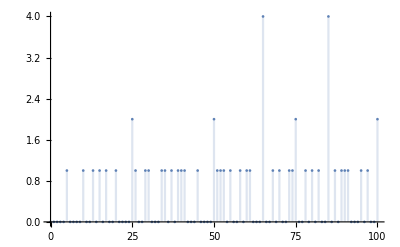

```mathematica
DiscretePlot[Floor[numpoints2D[Sqrt[2]*e]/2],{e,0,100},PlotRange->Full]
```

```mathematica
points2D[Sqrt[2]*25]
```

{{5,35},{17,31},{25,25},{31,17},{35,5}}

From the graph above, 65 is the first non - trivial occurrence that has 4 different pairs. The central element must be a product of more than two distinct primes of the form 4k + 1, e.g. 65 = (5)(13).

```mathematica
FactorInteger[65]
```

{{5,1},{13,1}}

```mathematica
points2D[Sqrt[2]*65]
```

{{13,91},{23,89},{35,85},{47,79},{65,65},{79,47},{85,35},{89,23},{91,13}}

We can therefore immediately write down a square that works for the central rows, colums and main diagonals, but that is not guaranteed to work with the perimeter rows and columns.
13^2 | 23^2 | 47^2
35^2 | 65^2 | 85^2
79^2 | 89^2 | 91^2

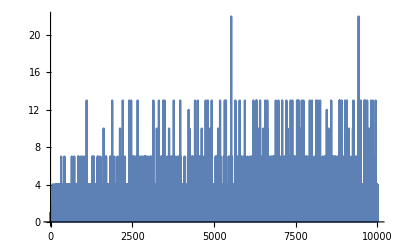

```mathematica
DiscretePlot[Floor[numpoints2D[Sqrt[2]*n]/2],{n,0,10000},PlotRange->Full]
```

```mathematica
CheckPerimeter[pointse_]:= Module[{bfound,p,i},Do[
bfound=False;
sqsums=points2D[Sqrt[2]*p][[1;;Floor[numpoints2D[Sqrt[2]*p]/2]]];
For[i=1,i≤ Length[sqsums], i++,booltest=Complement[sqsums[[i]],pointse]==={}; If[booltest, bfound=True;Print[Row[{p,";",sqsums[[i]]}]],]];,
{p,pointse}];
bfound]
```

Search for possible central elements e:

```mathematica
For[j=1,j≤10000,j++,
If[Floor[numpoints2D[Sqrt[2]*j]/2]>4,
If[CheckPerimeter[Flatten[points2D[Sqrt[2]*j][[1;;Floor[numpoints2D[Sqrt[2]*j]/2]]]]],Print[Row[{j,",",Floor[numpoints2D[Sqrt[2]*j]/2],",",}]],],]]
```

None found. Thus, we have a lower bound of e > 10000.

```mathematica
Monitor[For[j=10000,j≤1000000,j++,
If[Floor[numpoints2D[Sqrt[2]*j]/2]>4,
If[CheckPerimeter[Flatten[points2D[Sqrt[2]*j][[1;;Floor[numpoints2D[Sqrt[2]*j]/2]]]]],Print[Row[{j,",",Floor[numpoints2D[Sqrt[2]*j]/2],",",}]],],]],j]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

Thus, we have a lower bound of e > 21100 before the computer runs out of memory at e = 21125.

While our search above indicates that e = 5525 cannot work, we could of course write down the following only partially valid square:
365^2 | 833^2 | 1835^2
7565^2 | 5525^2 | 1955^2
7595^2 | 7769^2 | 7805^2